```mathematica
Length[f1m00]
```

88

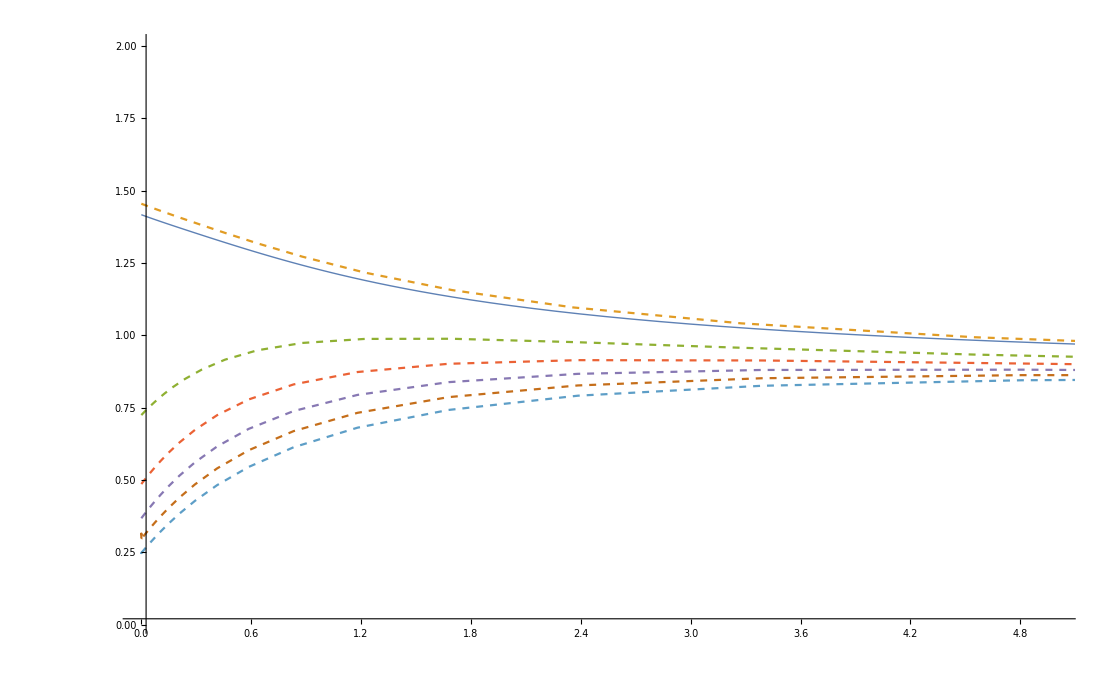

```mathematica
f1m00 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/f1m0.dat"];
f1m10 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/f1m1.dat"];
f1m20 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/f1m2.dat"];
f1m30 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/f1m3.dat"];
f1m40 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/f1m4.dat"];
f1m50 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/f1m5.dat"];
f1m60 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/f1m6.dat"];
f1m70 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/f1m7.dat"];
f1m80 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/f1m8.dat"];
f1m90 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/f1m9.dat"];
f1m100 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/f1m10.dat"];
f1m110 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/f1m11.dat"];
a = Import["/home/sigfried/MEGA/Dropbox/GapEqn/a_p_Q.dat"];
ListPlot[{a,f1m00,f1m10,f1m20,f1m30,f1m40,f1m50},Joined->True,PlotRange->{{0.001,5},{0.01,2}},PlotStyle->{Thick,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Thick}]
```

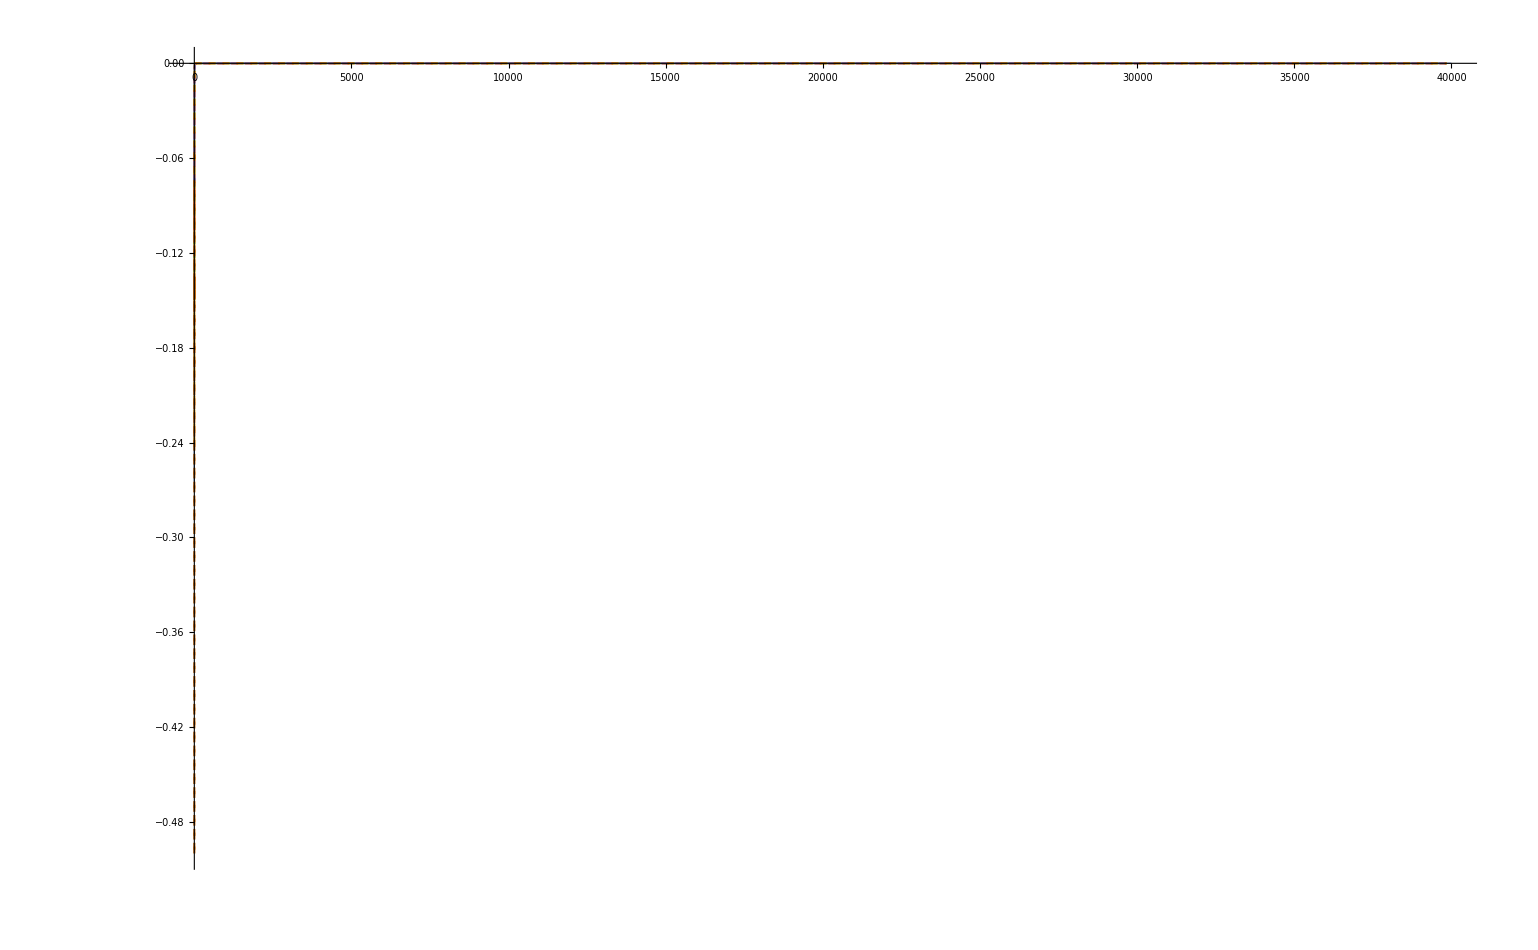

```mathematica
f2m00 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/f2m0.dat"];
f2m10 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/f2m1.dat"];
f2m20 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/f2m2.dat"];
f2m30 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/f2m3.dat"];
f2m40 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/f2m4.dat"];
f2m50 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/f2m5.dat"];
f2m60 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/f2m6.dat"];
f2m70 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/f2m7.dat"];
f2m80 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/f2m8.dat"];
f2m90 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/f2m9.dat"];
f2m100 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/f2m10.dat"];
f2m110 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/f2m11.dat"];
ap0 = Interpolation[a];
ap = Table[{a[[i,1]],ap0'[a[[i,1]]]},{i,1,Length[a]}];


ListPlot[{ap,f2m00,f2m10,f2m20,f2m30,f2m40},Joined->True,PlotRange->{{0.001,7},{0.0001,-.5}},PlotStyle->{Thick,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Thick}]
```

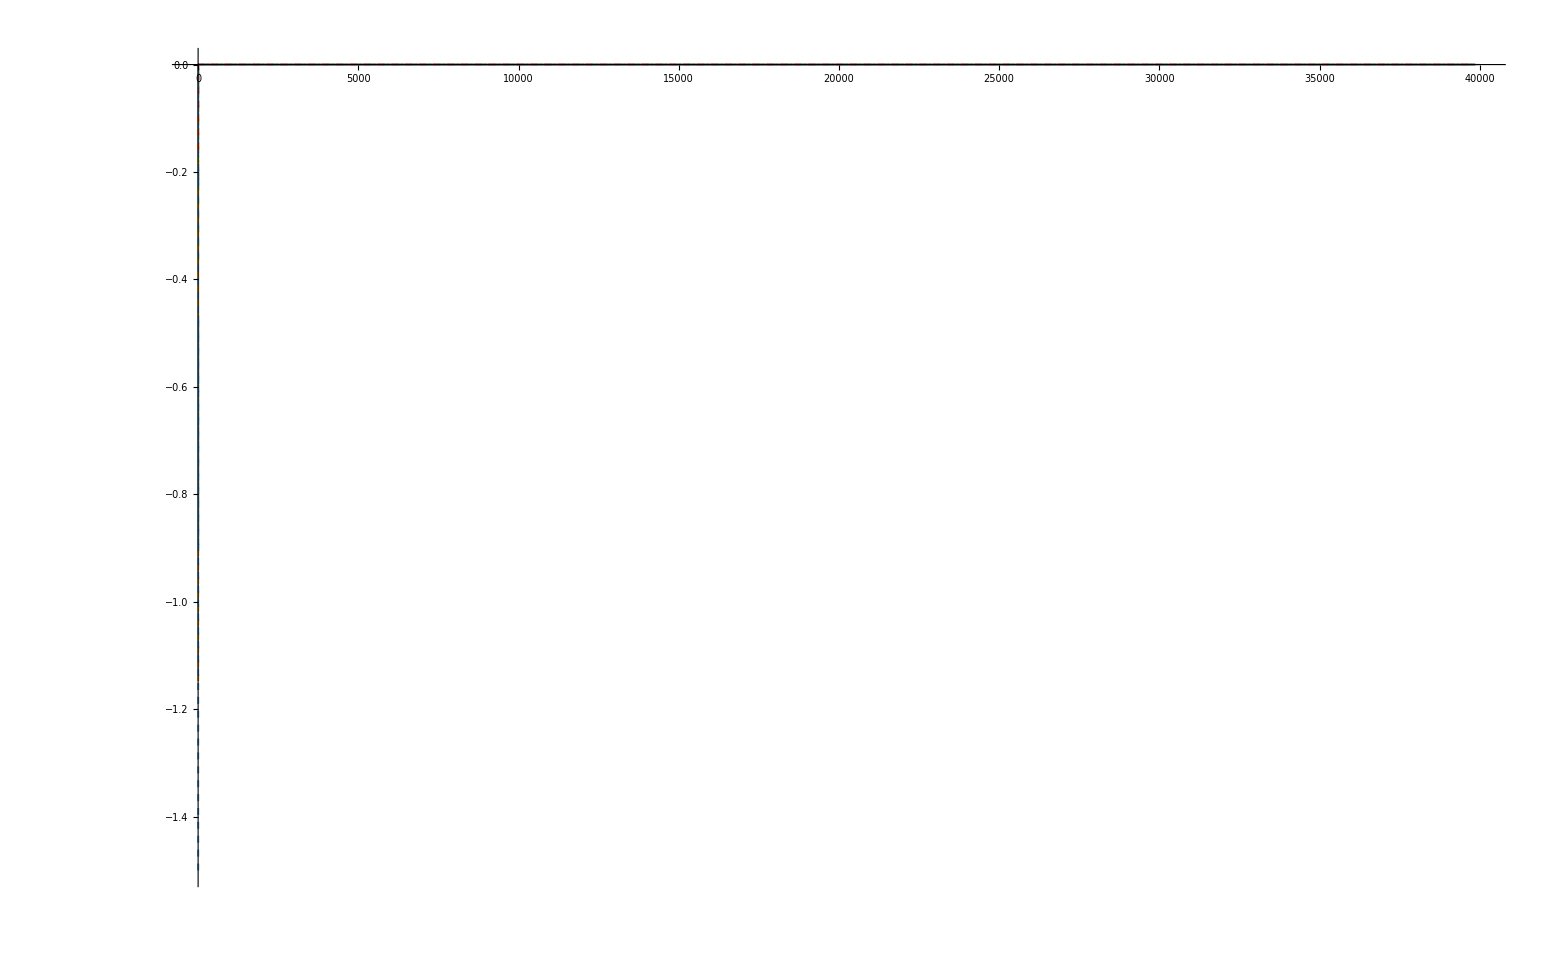

```mathematica
f3m00 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/f3m0.dat"];
f3m10 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/f3m1.dat"];
f3m20 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/f3m2.dat"];
f3m30 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/f3m3.dat"];
f3m40 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/f3m4.dat"];
f3m50 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/f3m5.dat"];
f3m60 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/f3m6.dat"];
f3m70 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/f3m7.dat"];
f3m80 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/f3m8.dat"];
f3m90 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/f3m9.dat"];
f3m100 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/f3m10.dat"];
f3m110 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/f3m11.dat"];
bpp = Import["/home/sigfried/MEGA/Dropbox/GapEqn/b_p_Q.dat"];
bp0 = Interpolation[bpp];
bp = Table[{bpp[[i,1]],bp0'[bpp[[i,1]]]},{i,1,Length[bpp]}];



ListPlot[{bp,f3m00,f3m10,f3m20,f3m30,f3m40,f3m50},Joined->True,PlotRange->{{0.001,4},{0.0001,-1.5}},PlotStyle->{Thick,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Thick}]
```

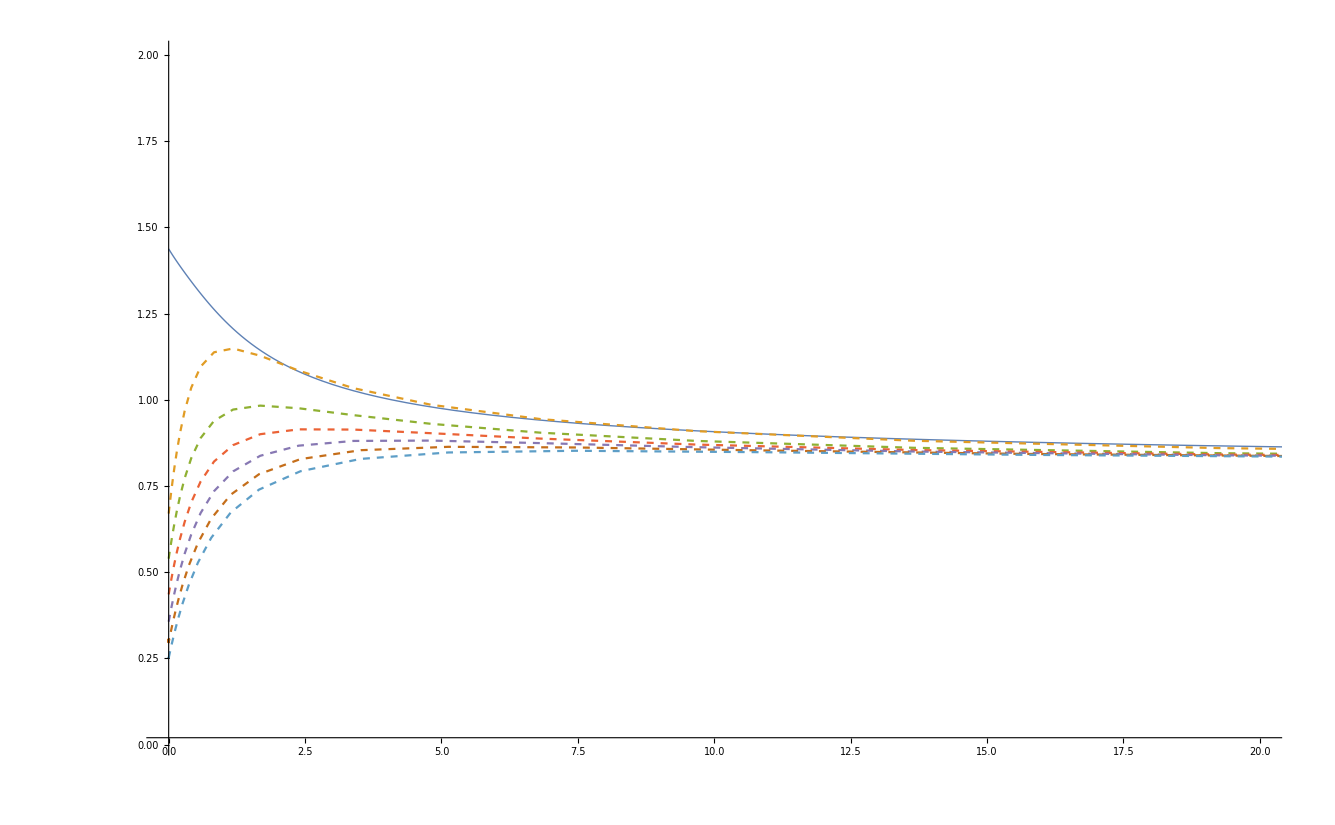

```mathematica
h1m00 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/h1m0.dat"];
h1m10 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/h1m1.dat"];
h1m20 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/h1m2.dat"];
h1m30 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/h1m3.dat"];
h1m40 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/h1m4.dat"];
h1m50 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/h1m5.dat"];
h1m60 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/h1m6.dat"];
h1m70 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/h1m7.dat"];
h1m80 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/h1m8.dat"];
h1m90 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/h1m9.dat"];
h1m100 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/h1m10.dat"];
h1m110 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/h1m11.dat"];
a = Import["/home/sigfried/MEGA/Dropbox/GapEqn/a_p_Q.dat"];
ListPlot[{a,h1m00,h1m10,h1m20,h1m30,h1m40,h1m50},Joined->True,PlotRange->{{-0.00001,20},{0.01,2}},PlotStyle->{Thick,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Thick}]
```

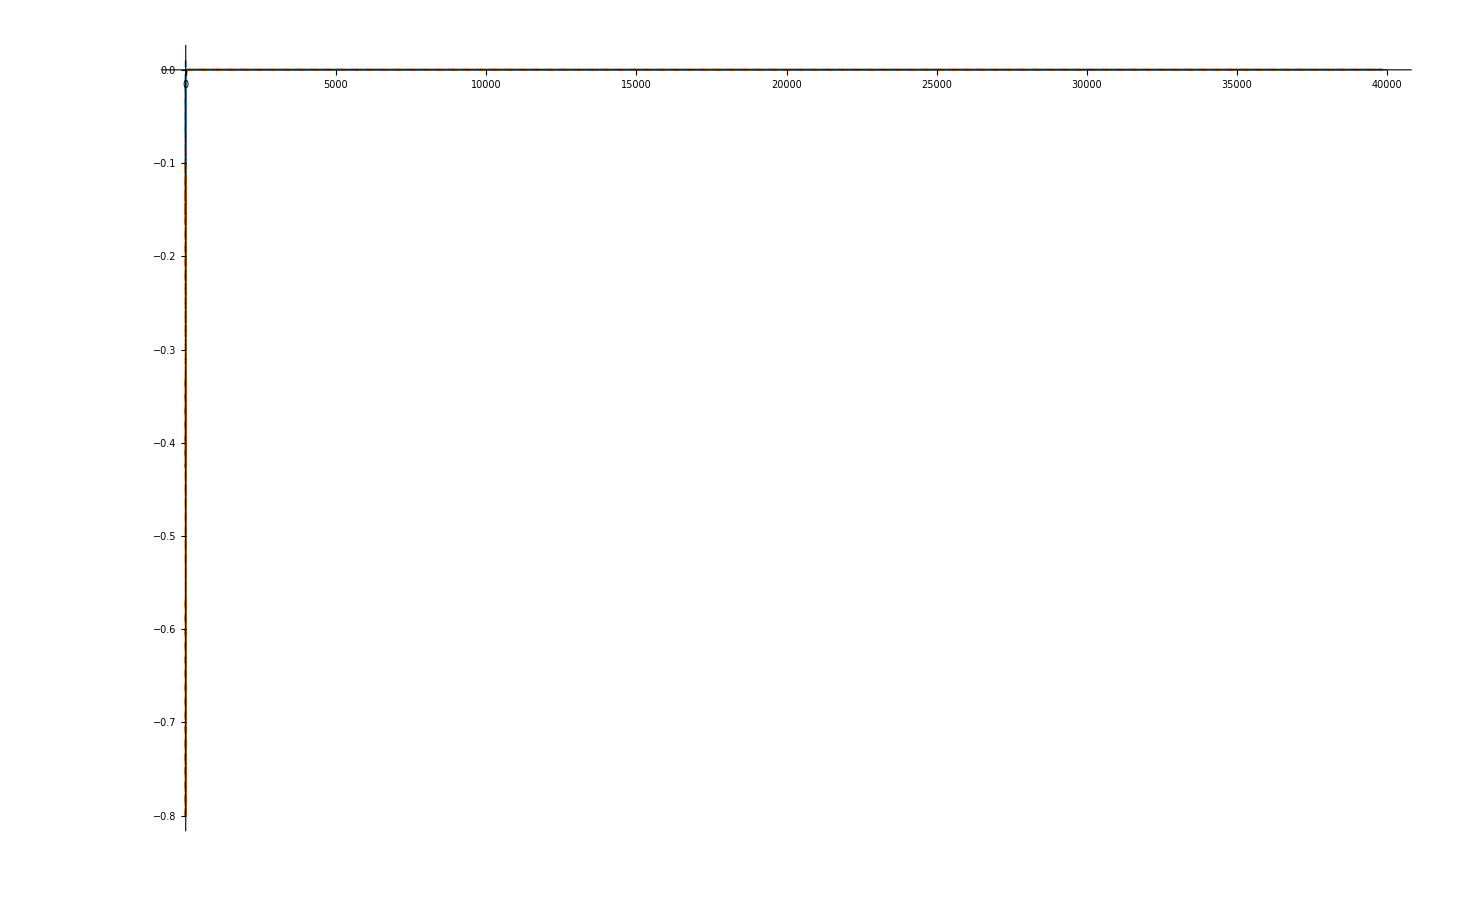

```mathematica
h2m00 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/h2m0.dat"];
h2m10 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/h2m1.dat"];
h2m20 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/h2m2.dat"];
h2m30 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/h2m3.dat"];
h2m40 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/h2m4.dat"];
h2m50 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/h2m5.dat"];
h2m60 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/h2m6.dat"];
h2m70 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/h2m7.dat"];
h2m80 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/h2m8.dat"];
h2m90 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/h2m9.dat"];
h2m100 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/h2m10.dat"];
h2m110 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/h2m11.dat"];
a = Import["/home/sigfried/MEGA/Dropbox/GapEqn/a_p_Q.dat"];
ListPlot[{ap,h2m00,h2m10,h2m20,h2m30,h2m40,h2m50},Joined->True,PlotRange->{{0.00001,4},{0.01,-.8}},PlotStyle->{Thick,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Thick}]
```

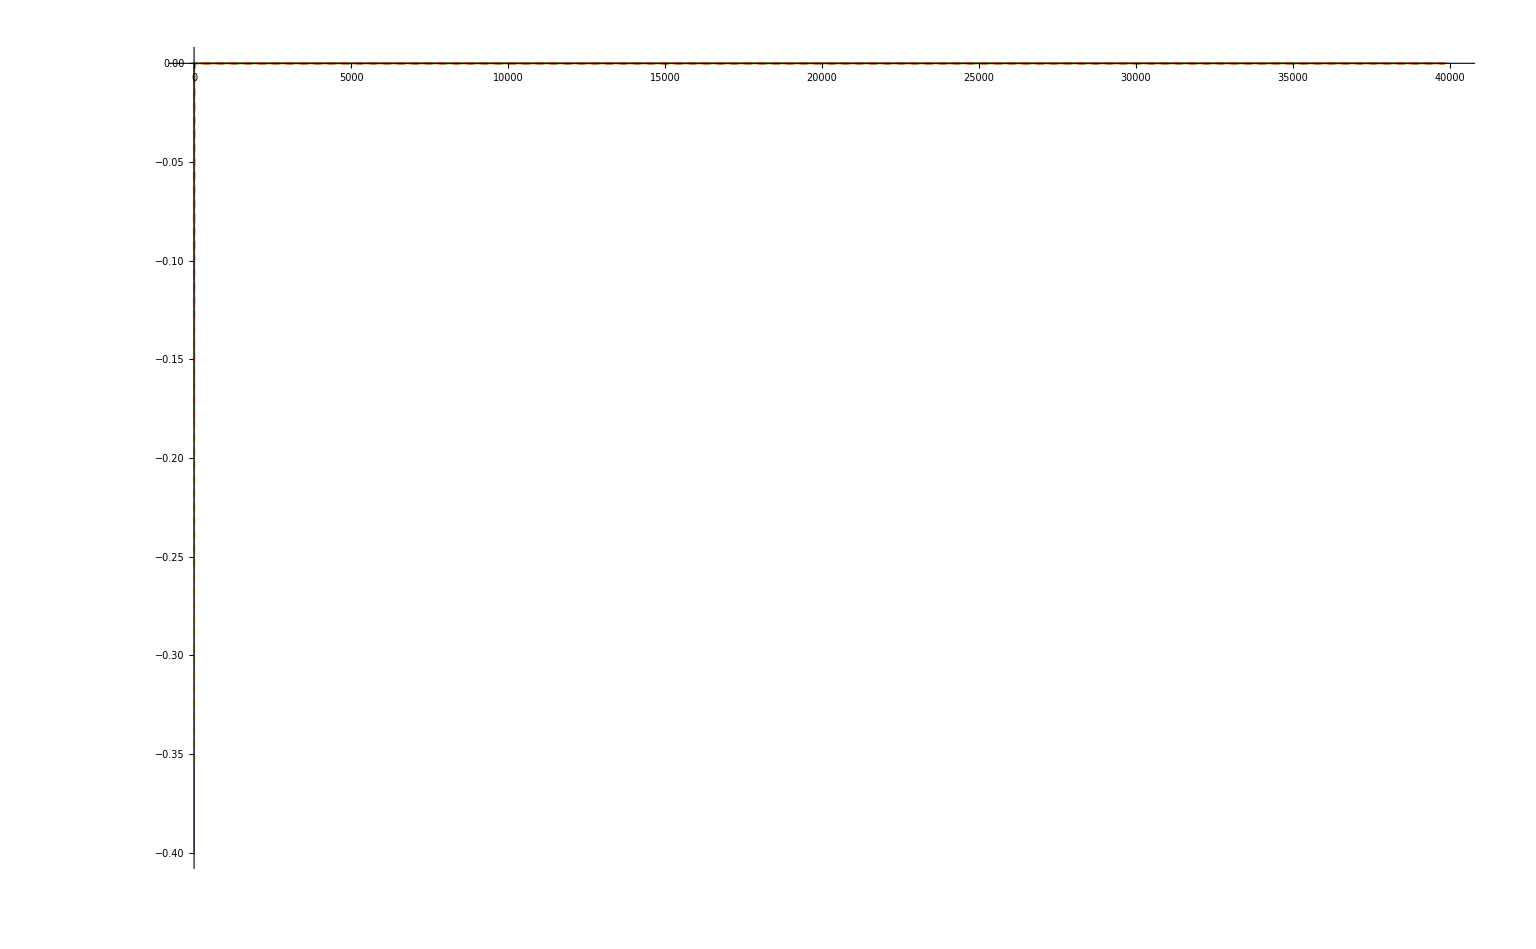

```mathematica
h3m00 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/h3m0.dat"];
h3m10 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/h3m1.dat"];
h3m20 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/h3m2.dat"];
h3m30 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/h3m3.dat"];
h3m40 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/h3m4.dat"];
h3m50 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/h3m5.dat"];
h3m60 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/h3m6.dat"];
h3m70 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/h3m7.dat"];
h3m80 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/h3m8.dat"];
h3m90 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/h3m9.dat"];
h3m100 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/h3m10.dat"];
h3m110 = Import["/home/sigfried/MEGA/Dropbox/GapEqn/h3m11.dat"];
a = Import["/home/sigfried/MEGA/Dropbox/GapEqn/a_p_Q.dat"];
ListPlot[{bp,h3m00,h3m10,h3m20,h3m30,h3m40},Joined->True,PlotRange->{{0.00001,4},{0.01,-.4}},PlotStyle->{Thick,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Thick}]
```